```mathematica
poly[n_]:=Table[{Cos[(2k-1)/n Pi],Sin[(2k-1)/n Pi]},{k,1,n}]
```

```mathematica
printPolygon[ls_]:=ListLinePlot[Append[ls,ls[[1]]],AspectRatio->1]
printPolygon[Fat[ls_]]:=ListLinePlot[Append[ls,ls[[1]]],AspectRatio->1,PlotStyle->Thickness[0.01]]
```

```mathematica
printPolygons[ls_]:=Show@@(printPolygon/@ls);
```

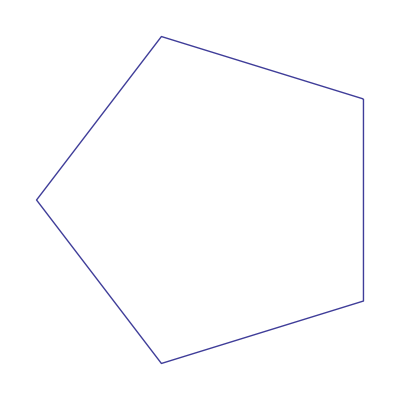

```mathematica
printPolygon[poly[5]]
```

```mathematica
rotateToMin[ls_]:=Module[{best=ls[[1]],bestI=1,cur,i},
For[i=1,i≤Length@ls,i++,
cur=ls[[i]];
If[cur[[2]]<best[[2]]||cur[[2]]==best[[2]]&&cur[[1]]<best[[1]],
best=cur;
bestI=i;
]
];
ls[[bestI;;]]~Join~ls[[;;bestI-1]]
]
```

```mathematica
Clear@angle;
angle=Compile[{{p1,_Real,1},{p2,_Real,1}},
Module[{x1,y1,x2,y2,a},
{x1,y1}=p1;
{x2,y2}=p2;
a=ArcTan[x2-x1,y2-y1];
If[a<0,a+=2Pi];
a
]
];
```

```mathematica
Clear@minkowskiSum;
minkowskiSum[p_,r_]:=Module[{
n=Length@p,m=Length@r,
p2=p~Join~p,
r2=(*(#-r[[1]])&/@*)r~Join~r,
i=1,j=1,
res={}
},
While[i≠n+1||j≠m+1,
AppendTo[res,p2[[i]]+r2[[j]]];
If[angle[p2[[i]],p2[[i+1]]]<angle[r2[[j]],r2[[j+1]]]&&i≠n+1,
i+=1,
If[angle[p2[[i]],p2[[i+1]]]>angle[r2[[j]],r2[[j+1]]]&&j≠m+1,
j+=1,
If[i<n+1,i+=1];If[j<m+1,j+=1]
]
]
];
res
]
```

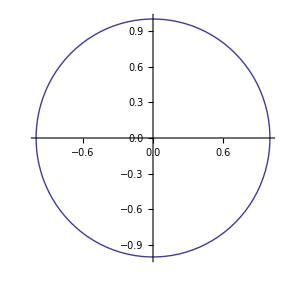

```mathematica
printPolygon[poly[100]]
```

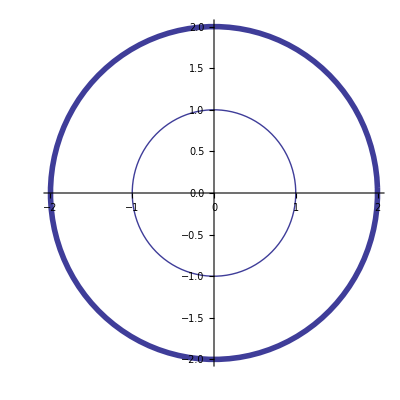

```mathematica
printPolygons[{Fat@minkowskiSum[poly[100],poly[100]],poly[100]}]
```

```mathematica
unitSquare={{0,0},{1,0},{1,1},{0,1}};
```

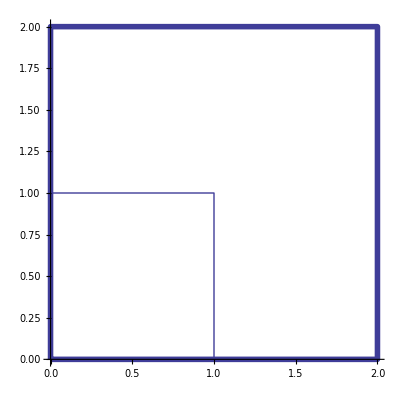

```mathematica
printPolygons[{Fat@minkowskiSum[unitSquare,unitSquare],unitSquare}]
```

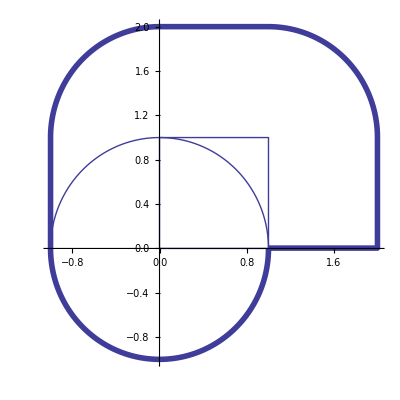

```mathematica
printPolygons[{Fat@minkowskiSum[poly[1000],unitSquare],poly[1000],unitSquare}]
```

```mathematica
triangle={{0,0},{1,0},{0,1}};
```

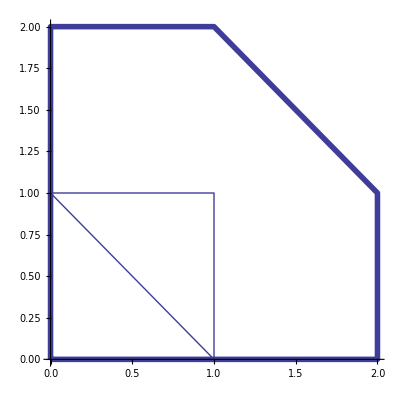

```mathematica
printPolygons[{Fat@minkowskiSum[triangle,unitSquare],triangle,unitSquare}]
```